```mathematica
Eigensystem[{{0, I, -I, 0},{I, -G, 0, -I},{-I,0,-G,I},{0,-I,I,-2G}}]
```

{{-G,-G,-G-√(-4+G^2),-G+√(-4+G^2)},{{1,ⅈ G,0,1},{0,1,1,0},{1/2 (-2+G^2-G √(-4+G^2)),(ⅈ (4-G^2+G √(-4+G^2)))/(2 √(-4+G^2)),-(ⅈ (4-G^2+G √(-4+G^2)))/(2 √(-4+G^2)),1},{1/2 (-2+G^2+G √(-4+G^2)),(ⅈ (-4+G^2+G √(-4+G^2)))/(2 √(-4+G^2)),-(ⅈ (-4+G^2+G √(-4+G^2)))/(2 √(-4+G^2)),1}}}

```mathematica
l0[G_]:=-G+√(-4+G^2)
```

```mathematica
z
```

```mathematica
FullSimplify[{1/2 (-2+G^2+G √(-4+G^2)),(ⅈ (-4+G^2+G √(-4+G^2)))/(2 √(-4+G^2)),-(ⅈ (-4+G^2+G √(-4+G^2)))/(2 √(-4+G^2)),1}/(1/2 (-2+G^2+G √(-4+G^2))+1), Assumptions->{G>0}]
```

{(G+√(-4+G^2))/(2 G),ⅈ/G,-ⅈ/G,2/(G^2+G √(-4+G^2))}

```mathematica
FullSimplify[-Log2[(1 +(Sqrt[1-4/G^2])^4 +(-2/G)^4)/2]]
```

-Log[1-(4 (-4+G^2))/G^4]/Log[2]

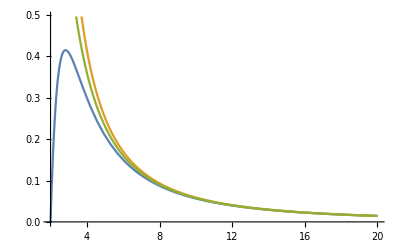

```mathematica
Plot[{-Log[1-(4 (-4+G^2))/G^4]/Log[2], -Log[1-4/G^2]/Log[2], (4/G^2)/Log[2]},{G,2,20}]
```

```mathematica
FullSimplify[D[-Log[1-(4 (-4+G^2))/G^4]/Log[2], G], Assumptions->{G>0}]
```

-(8 (-8+G^2))/(G (16-4 G^2+G^4) Log[2])

```mathematica
Solve[-(8 (-8+G^2))/(G (16-4 G^2+G^4) Log[2])==0, G]
```

{{G→-2 √2},{G→2 √2}}

```mathematica
-Log[1-(4 (-4+G^2))/G^4]/Log[2]/.{G->2Sqrt[2]}
```

Log[4/3]/Log[2]

```mathematica
N[Log[4/3]/Log[2]]
```

0.415037

```mathematica
H[G_]:={{0, (1-I)/Sqrt[2]},{(1+I)/Sqrt[2], -I G}}
FullSimplify[Eigenvalues[H[G]], Assumptions->{G>0}]
```

{(-1/4-ⅈ/4) ((1+ⅈ) G+√2 √(ⅈ (-4+G^2))),(1/4+ⅈ/4) ((-1-ⅈ) G+√2 √(ⅈ (-4+G^2)))}

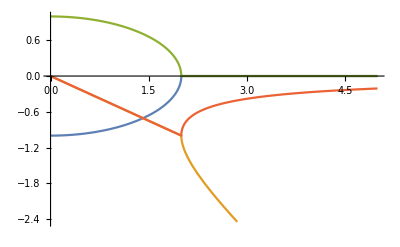

```mathematica
Plot[{Re[(-1/4-ⅈ/4) ((1+ⅈ) G+√2 √(ⅈ (-4+G^2)))], Im[(-1/4-ⅈ/4) ((1+ⅈ) G+√2 √(ⅈ (-4+G^2)))],Re[(1/4+ⅈ/4) ((-1-ⅈ) G+√2 √(ⅈ (-4+G^2)))], Im[(1/4+ⅈ/4) ((-1-ⅈ) G+√2 √(ⅈ (-4+G^2)))]}, {G, 0, 5}]
```

```mathematica
FullSimplify[-I KroneckerProduct[H[G],IdentityMatrix[2]]+I KroneckerProduct[IdentityMatrix[2],Conjugate[H[G]]], Assumptions->{G>0}]
```

{{0,(-1)^(3/4),-(-1)^(1/4),0},{(-1)^(1/4),-G,0,-(-1)^(1/4)},{-(-1)^(3/4),0,-G,(-1)^(3/4)},{0,-(-1)^(3/4),(-1)^(1/4),-2 G}}

```mathematica
Eigensystem[{{0,(-1)^(3/4),-(-1)^(1/4),0},{(-1)^(1/4),-G,0,-(-1)^(1/4)},{-(-1)^(3/4),0,-G,(-1)^(3/4)},{0,-(-1)^(3/4),(-1)^(1/4),-2 G}}]
```

{{-G,-G,-G-√(-4+G^2),-G+√(-4+G^2)},{{1,(-1)^(1/4) G,0,1},{0,-ⅈ,1,0},{1/2 (-2+G^2-G √(-4+G^2)),-(-4 (-1)^(1/4)+(-1)^(1/4) G^2-(-1)^(1/4) G √(-4+G^2))/(2 √(-4+G^2)),-(4 (-1)^(3/4)-(-1)^(3/4) G^2+(-1)^(3/4) G √(-4+G^2))/(2 √(-4+G^2)),1},{1/2 (-2+G^2+G √(-4+G^2)),-(4 (-1)^(1/4)-(-1)^(1/4) G^2-(-1)^(1/4) G √(-4+G^2))/(2 √(-4+G^2)),-(-4 (-1)^(3/4)+(-1)^(3/4) G^2+(-1)^(3/4) G √(-4+G^2))/(2 √(-4+G^2)),1}}}

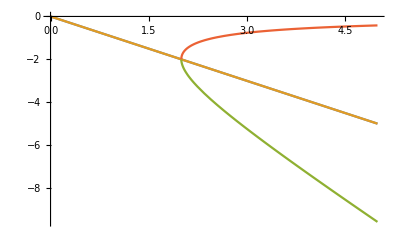

```mathematica
Plot[{-G,-G,-G-√(-4+G^2),-G+√(-4+G^2)}, {G, 0, 5}]
```

```mathematica
Eigensystem[{{0,(-1)^(3/4),-(-1)^(1/4),0},{(-1)^(1/4),A,0,-(-1)^(1/4)},{-(-1)^(3/4),0,A,(-1)^(3/4)},{0,-(-1)^(3/4),(-1)^(1/4),B}}]
```

{{A,Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1],Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2],Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]},{{0,-ⅈ,1,0},{-(-B+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1])/Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1],-(-1)^(1/4) B+(-1)^(1/4) Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]-((-1)^(1/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1])),-(((-1)^(3/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))),1},{-(-B+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2])/Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2],-(-1)^(1/4) B+(-1)^(1/4) Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2]-((-1)^(1/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2])),-(((-1)^(3/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2]))),1},{-(-B+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3])/Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3],-(-1)^(1/4) B+(-1)^(1/4) Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]-((-1)^(1/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3])),-(((-1)^(3/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]))),1}}}

```mathematica
FullSimplify[{1/2 (-2+G^2+G √(-4+G^2)),-(4 (-1)^(1/4)-(-1)^(1/4) G^2-(-1)^(1/4) G √(-4+G^2))/(2 √(-4+G^2)),-(-4 (-1)^(3/4)+(-1)^(3/4) G^2+(-1)^(3/4) G √(-4+G^2))/(2 √(-4+G^2)),1}/(1+1/2 (-2+G^2+G √(-4+G^2))), Assumptions->{G>2}]
```

{(G+√(-4+G^2))/(2 G),(-1)^(1/4)/G,-(-1)^(3/4)/G,2/(G^2+G √(-4+G^2))}

```mathematica
Im[(-1)^(3/4)]
```

1/(√2)

```mathematica
FullSimplify[-Log2[(1 +(Sqrt[1-4/G^2])^4 +(-Sqrt[2]/G)^4+(Sqrt[2]/G)^4)/2]]
```

-Log[1-(4 (-3+G^2))/G^4]/Log[2]

```mathematica
-Log[1-(4 (-3+G^2))/G^4]/Log[2]/.{G->2}
```

Log[4/3]/Log[2]

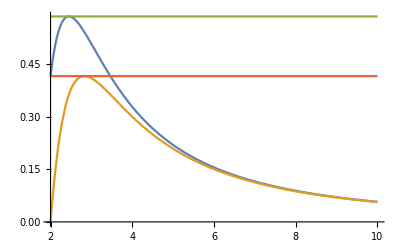

```mathematica
Plot[{-Log[1-(4 (-3+G^2))/G^4]/Log[2], -Log[1-(4 (-4+G^2))/G^4]/Log[2], Log2[3/2],  Log2[4/3]},{G,2,10}]
```

```mathematica
D[-Log[1-(4 (-3+G^2))/G^4]/Log[2], G]
```

-(-8/G^3+(16 (-3+G^2))/G^5)/((1-(4 (-3+G^2))/G^4) Log[2])

```mathematica
Solve[-(-8/G^3+(16 (-3+G^2))/G^5)/((1-(4 (-3+G^2))/G^4) Log[2])==0]
```

{{G→-√6},{G→√6}}

```mathematica
FullSimplify[-Log[1-(4 (-3+G^2))/G^4]/Log[2]/.{G->Sqrt[6]}]
```

Log[3/2]/Log[2]

```mathematica
N[Log[3/2]/Log[2]]
```

0.584963

```mathematica
Eigenvalues[{{0,(-1)^(3/4),-(-1)^(1/4),0},{(-1)^(1/4),A,0,-(-1)^(1/4)},{-(-1)^(3/4),0,A,(-1)^(3/4)},{0,-(-1)^(3/4),(-1)^(1/4),B}}]
```

{A,Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1],Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,2],Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,3]}

```mathematica
TeXForm[{{0,(-1)^(3/4),-(-1)^(1/4),0},{(-1)^(1/4),A,0,-(-1)^(1/4)},{-(-1)^(3/4),0,A,(-1)^(3/4)},{0,-(-1)^(3/4),(-1)^(1/4),B}}]
```

\left(
\begin{array}{cccc}
 0 & (-1)^{3/4} & -\sqrt[4]{-1} & 0 \\
 \sqrt[4]{-1} & A & 0 & -\sqrt[4]{-1} \\
 -(-1)^{3/4} & 0 & A & (-1)^{3/4} \\
 0 & -(-1)^{3/4} & \sqrt[4]{-1} & B \\
\end{array}
\right)

```mathematica
"PRL Li Chen, Abbasi, Murch, Whaley, Entanglement by proximity to EP"
η[O_,g_]:= Sqrt[16 O^2 - g^2]
χ[J_,g_,O_]:= J (η[O,g]^2+3 g^2)/η[O,g]^2
B[O_, g_,J_,t_]:= 16 O^2(g^2+32 O^2) + g(g(g^2-η[O,g]^2)Cos[t η[O,g]]-2 g^2 η[O,g]Sin[t η[O,g]]-64 O^2 Cos[t χ[J,g,O]/2](g Cos[t η[O,g]/2]- η[O,g] Sin[t η[O,g]/2]))
```

```mathematica
con[t_,O_,g_,J_]:=Abs[16 η[O,g]^2 O^2 (Exp[I t χ[J,g,O]]-1)/B[O,g,J,t]]
```

```mathematica
Manipulate[LogPlot[con[t,1.6,g,0.001],{t, 0, 10}, PlotRange->{0.0001,1}],{g,0.00001,6}]
```

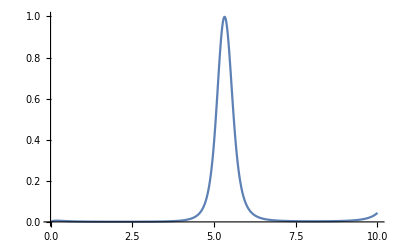

```mathematica
Plot[con[t,1.6,6,  10^(-3)],{t, 0, 10}, PlotRange->{0, 1}]
```

```mathematica
FullSimplify[Solve[{Exp[I 3 Pi/4] b1 + Exp[-I 3 Pi/4]b2 == l b0,Exp[I Pi/4] b0 + Exp[-I 3 Pi/4]b3 == (l-A) b1,Exp[-I Pi/4] b0 + Exp[+I 3 Pi/4]b3 == (l-A) b2,Exp[-I Pi/4] b1 + Exp[I Pi/4]b2 == (l-b) b3, b0+b3 ==1},{b0,b1,b2,b3}], Assumptions->{b0>0, b3>0, Element[l, Reals], l>A, l > b}]
```

{}

```mathematica
Cos[3 Pi/4]
```

-1/(√2)

```mathematica
b3[l_, A_, B_]:= (2 + l (l-A))/(4 + (l-A)(2 l - B))
b0[l_, A_, B_]:= (2 + (l-B) (l-A))/(4 + (l-A)(2 l - B))
```

```mathematica
Clear[B]
```

```mathematica
FullSimplify[1/(2 Sqrt[2])((l - B)b3[l,A,B]- l b0[l,A,B])]
```

B/(√2 (-4+(B-2 l) (-A+l)))

```mathematica
Simplify[-1/(2 Sqrt[2])((l - B)b3[l,A,B]+ l b0[l,A,B])]
```

(B (1-A l+l^2)-l (2-A l+l^2))/(√2 (4+A (B-2 l)-B l+2 l^2))

```mathematica
MatrixForm[{-(-B+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1])/Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1],-(-1)^(1/4) B+(-1)^(1/4) Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]-((-1)^(1/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1])),-(((-1)^(3/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))),1}]
```

(-(-B+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1])/Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]
-(-1)^(1/4) B+(-1)^(1/4) Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]-((-1)^(1/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))
-((-1)^(3/4) (B-2 Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))/(Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1] (-A+Root[-2 B+(4+A B) #1+(-A-B) #1^2+#1^3&,1]))
1)

```mathematica
FullSimplify[-(-1)^(1/4) B+(-1)^(1/4)l-((-1)^(1/4) (B-2l ))/(l (-A+l)), Assumptions->{l>0, B>0, A>0, -2 B+(4+A B)l+(-A-B)l^2+l^3==0}]
```

((-1)^(1/4) (B-2 l))/(l (-A+l))

```mathematica
FullSimplify[{(B-l)/l, ((-1)^(1/4) (B-2 l))/(l (-A+l)), Conjugate[((-1)^(1/4) (B-2 l))/(l (-A+l))], 1}l/B,  Assumptions->{l>0, B>0, A>0}]
```

{1-l/B,((-1)^(1/4) (B-2 l))/(B (-A+l)),((-1)^(3/4) (B-2 l))/(B (A-l)),l/B}

```mathematica
TeXForm[{1-l/B,((-1)^(1/4) (B-2 l))/(B (-A+l)),((-1)^(3/4) (B-2 l))/(B (A-l)),l/B}/.{l->Subscript[λ, 0]}]
```

\left\{1-\frac{\lambda _0}{B},\frac{\sqrt[4]{-1} \left(B-2 \lambda _0\right)}{B \left(\lambda _0-A\right)},\frac{(-1)^{3/4} \left(B-2 \lambda
   _0\right)}{B \left(A-\lambda _0\right)},\frac{\lambda _0}{B}\right\}

```mathematica
Sin[3 Pi/4]
```

1/(√2)

```mathematica
x[A_,B_,l_]:= Sqrt[2](B- 2 l)/(B (l - A))
y[A_,B_,l_]:= -Sqrt[2](B- 2 l)/(B (l - A))
z[A_,B_,l_]:= (B- 2 l)/(B)
```

```mathematica
FullSimplify[(1 + x[A,B,l]^4+ y[A,B,l]^4+ z[A,B,l]^4)/(1 + x[A,B,l]^2+ y[A,B,l]^2+ z[A,B,l]^2), Assumptions->{A>0,B>0, l>0, A-l>0}]
```

(1+(B-2 l)^4/B^4+(8 (B-2 l)^4)/(B^4 (A-l)^4))/(1+(B-2 l)^2/B^2+(4 (B-2 l)^2)/(B^2 (A-l)^2))

```mathematica
Fu
```

```mathematica
N[Log2[5]-2]
```

0.321928

```mathematica
Clear[x,y,z]
```

```mathematica
rho0[x_,y_,z_]:= {{1+z, x - I y},{x+ I y, 1 - z}}/2
```

```mathematica
H[J_,G_]:= {{0, J},{J,-I G}}
prop[t_,J_,G_]=FullSimplify[MatrixExp[-I H[J,G]t], Assumptions->{G>0, J>0,  G^2-4J^2<0}]
```

{{ⅇ^(-(G t)/2) (Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))),(2 ⅇ^(-(G t)/2) J Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))},{(2 ⅇ^(-(G t)/2) J Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2)),ⅇ^(-(G t)/2) (Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2)))}}

```mathematica
urhot[t_,J_,G_,x_,y_,z_]=prop[t, J, G].rho0[x,y,z].ConjugateTranspose[prop[t,J,G]]
```

{{ⅇ^(-1/2 Conjugate[G t]) Conjugate[Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))] ((ⅇ^(-(G t)/2) J (x+ⅈ y) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (1+z) (Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))))+2 ⅇ^(-1/2 Conjugate[G t]) Conjugate[J/(√(G^2-4 J^2))] ((ⅇ^(-(G t)/2) J (1-z) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (x-ⅈ y) (Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2)))) Sin[1/2 Conjugate[√(-G^2+4 J^2) t]],ⅇ^(-1/2 Conjugate[G t]) Conjugate[Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))] ((ⅇ^(-(G t)/2) J (1-z) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (x-ⅈ y) (Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))))+2 ⅇ^(-1/2 Conjugate[G t]) Conjugate[J/(√(G^2-4 J^2))] ((ⅇ^(-(G t)/2) J (x+ⅈ y) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (1+z) (Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2)))) Sin[1/2 Conjugate[√(-G^2+4 J^2) t]]},{ⅇ^(-1/2 Conjugate[G t]) Conjugate[Cos[1/2 √(-G^2+4 J^2) t]+(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))] ((ⅇ^(-(G t)/2) J (1+z) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (x+ⅈ y) (Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))))+2 ⅇ^(-1/2 Conjugate[G t]) Conjugate[J/(√(G^2-4 J^2))] ((ⅇ^(-(G t)/2) J (x-ⅈ y) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (1-z) (Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2)))) Sin[1/2 Conjugate[√(-G^2+4 J^2) t]],ⅇ^(-1/2 Conjugate[G t]) Conjugate[Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))] ((ⅇ^(-(G t)/2) J (x-ⅈ y) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (1-z) (Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2))))+2 ⅇ^(-1/2 Conjugate[G t]) Conjugate[J/(√(G^2-4 J^2))] ((ⅇ^(-(G t)/2) J (1+z) Sin[1/2 √(-G^2+4 J^2) t])/(√(G^2-4 J^2))+1/2 ⅇ^(-(G t)/2) (x+ⅈ y) (Cos[1/2 √(-G^2+4 J^2) t]-(G Sin[1/2 √(-G^2+4 J^2) t])/(√(-G^2+4 J^2)))) Sin[1/2 Conjugate[√(-G^2+4 J^2) t]]}}

```mathematica
rhot[t_,J_,G_,x_,y_,z_]=FullSimplify[ urhot[t, J, G,x,y,z]/ Tr[urhot[t, J, G,x,y,z]]]
```

{{-(-2 J (2 J+G y)+(2 G J y-4 J^2 z+G^2 (1+z)) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y+G z) Sinh[√(G^2-4 J^2) t])/(4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]),(2 ⅈ G J+4 J^2 x-G^2 (x-ⅈ y)-2 ⅈ J ((G+2 J y) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]))/(4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])},{(-2 ⅈ G J+4 J^2 x-G^2 (x+ⅈ y)+2 ⅈ J ((G+2 J y) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]))/(4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]),(2 J (2 J+G y)+(-2 G J y+G^2 (-1+z)-4 J^2 z) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y-G z) Sinh[√(G^2-4 J^2) t])/(4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])}}

```mathematica
xt[t_, J_,G_,x_,y_,z_]=FullSimplify[2 Re[rhot[t,J,G,x,y,z][[1,2]]], Assumptions->{G t >0, G^2-4J^2!=0, Sqrt[G^2-4J^2]>0, G>0,J>0, Element[G+2 J y,Reals], t>0, x>-1, y>-1, z>-1, 4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]!=0}]
yt[t_, J_,G_,x_,y_,z_]=-FullSimplify[2 Im[rhot[t,J,G,x,y,z][[1,2]]], Assumptions->{G t >0, G^2-4J^2!=0, Sqrt[G^2-4J^2]>0, G>0,J>0, Element[G+2 J y,Reals], t>0, x>-1, y>-1, z>-1, 4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]!=0}]
zt[t_, J_,G_,x_,y_,z_]=FullSimplify[2 rhot[t,J,G,x,y,z][[1,1]]-1, Assumptions->{G t >0, G^2-4J^2!=0, Sqrt[G^2-4J^2]>0, G>0,J>0, Element[G+2 J y,Reals], t>0, x>-1, y>-1, z>-1, 2 J (2 J+G y)-G (G+2 J y) Cosh[√(G^2-4 J^2) t]-G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]!=0}]
```

((G^2-4 J^2) x)/(-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])

-(2 (2 G J+G^2 y-2 J ((G+2 J y) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])))/(4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])

-((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])/(2 J (2 J+G y)-G (G+2 J y) Cosh[√(G^2-4 J^2) t]-G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])

```mathematica
M2[t_,J_,G_,x_,y_,z_]=-Log2[(1 + xt[t,J,G,x,y,z]^4+ yt[t,J,G,x,y,z]^4+ zt[t,J,G,x,y,z]^4)/(1 + xt[t,J,G,x,y,z]^2+ yt[t,J,G,x,y,z]^2+ zt[t,J,G,x,y,z]^2)]
```

-1/Log[2]Log[(1+(((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^4)/((2 J (2 J+G y)-G (G+2 J y) Cosh[√(G^2-4 J^2) t]-G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4)+((G^2-4 J^2)^4 x^4)/((-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4)+(16 (2 G J+G^2 y-2 J ((G+2 J y) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]))^4)/((4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4))/(1+(((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^2)/((2 J (2 J+G y)-G (G+2 J y) Cosh[√(G^2-4 J^2) t]-G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2)+((G^2-4 J^2)^2 x^2)/((-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2)+(4 (2 G J+G^2 y-2 J ((G+2 J y) Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]))^2)/((4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2))]

```mathematica
Series[M2[t, 1, Sqrt[8], 0, 0, 0], {t,Infinity, 1}]
```

-1/Log[2]Log[1/(1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2))+16384/((8-16 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))-(65536 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))+(98304 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))-(65536 Cosh[2 t+O[1/t]^2]^3)/((8-16 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))+(16384 Cosh[2 t+O[1/t]^2]^4)/((8-16 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))+(1024 Sinh[2 t+O[1/t]^2]^4)/((4-8 Cosh[2 t+O[1/t]^2])^4 (1+128/((8-16 Cosh[2 t+O[1/t]^2])^2)-(256 Cosh[2 t+O[1/t]^2])/((8-16 Cosh[2 t+O[1/t]^2])^2)+(128 Cosh[2 t+O[1/t]^2]^2)/((8-16 Cosh[2 t+O[1/t]^2])^2)+(32 Sinh[2 t+O[1/t]^2]^2)/((4-8 Cosh[2 t+O[1/t]^2])^2)))]

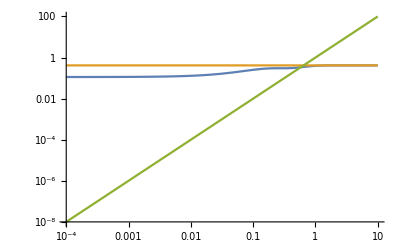

```mathematica
LogLogPlot[{M2[t,1,Sqrt[8],0, 0, 0], Log2[4/3], t^2},{t, 0.0001, 10}, PlotRange->Full]
```

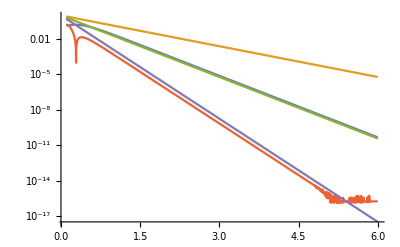

```mathematica
LogPlot[{Abs[M2[t,1,Sqrt[8],0, 0.1, 0.4]- Log2[4/3]], Exp[-2 t], Exp[-4t], Abs[M2[7,1,7,0, 0, 0]-M2[t,1,7,0, 0, 0]], Exp[-Sqrt[7^2-4]t]},{t, 0.1, 6}, PlotRange->Full]
```

```mathematica
psi0[θ_,ϕ_]:= {Cos[θ], Sin[θ]Exp[I ϕ]}
```

```mathematica
FullSimplify[(1 + xt[t,J,G,x,y,z]^4+ yt[t,J,G,x,y,z]^4+ zt[t,J,G,x,y,z]^4)/(1 + xt[t,J,G,x,y,z]^2+ yt[t,J,G,x,y,z]^2+ zt[t,J,G,x,y,z]^2), Assumptions->{G t >0, G^2-4J^2>0, Sqrt[G^2-4J^2]>0, G>0,J>0, Element[G+2 J y,Reals], t>0, x>-1, y>-1, z>-1, 2 J (2 J+G y)-G (G+2 J y) Cosh[√(G^2-4 J^2) t]-G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]!=0, 4 J (2 J+G y)-2 G (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]!=0}]
```

((G^2-4 J^2)^4 x^4+((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^4+(-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4+(G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4)/((-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2 ((G^2-4 J^2)^2 x^2+((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^2+(-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2+(G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2))

```mathematica
((G^2-4 J^2)^4 x^4+((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^4+(-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4+(G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^4)/((-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2 ((G^2-4 J^2)^2 x^2+((G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t])^2+(-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2+(G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t])^2))/.{√(G^2-4 J^2)->ω, G^2-4 J^2->ω^2, G-> Γ, -2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]-> f[t], G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]-> h[t], (G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t] -> k[t]}
```

(x^4 ω^8+f[t]^4+h[t]^4+k[t]^4)/(f[t]^2 (x^2 ω^4+f[t]^2+h[t]^2+k[t]^2))

```mathematica
TeXForm[(x^4 ω^8+f[t]^4+h[t]^4+k[t]^4)/(f[t]^2 (x^2 ω^4+f[t]^2+h[t]^2+k[t]^2))]
```

\frac{f(t)^4+h(t)^4+k(t)^4+x^4 \omega ^8}{f(t)^2 \left(f(t)^2+h(t)^2+k(t)^2+x^2 \omega ^4\right)}

```mathematica
-2 J (2 J+G y)+G (G+2 J y) Cosh[√(G^2-4 J^2) t]+G √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]/.{√(G^2-4 J^2)->ω, G^2-4 J^2->ω^2, G-> Γ}
```

-2 J (2 J+y Γ)+Γ (2 J y+Γ) Cosh[t ω]+z Γ ω Sinh[t ω]

```mathematica
TeXForm[-2 J (2 J+y Γ)+Γ (2 J y+Γ) Cosh[t ω]+z Γ ω Sinh[t ω]]
```

\Gamma  (\Gamma +2 J y) \cosh (t \omega )-2 J (2 J+\Gamma  y)+\Gamma  \omega  z \sinh (t \omega )

```mathematica
G (2 J+G y)-2 J (G+2 J y) Cosh[√(G^2-4 J^2) t]-2 J √(G^2-4 J^2) z Sinh[√(G^2-4 J^2) t]/.{√(G^2-4 J^2)->ω, G^2-4 J^2->ω^2, G-> Γ}
(G^2-4 J^2) z Cosh[√(G^2-4 J^2) t]+√(G^2-4 J^2) (G+2 J y) Sinh[√(G^2-4 J^2) t]/.{√(G^2-4 J^2)->ω, G^2-4 J^2->ω^2, G-> Γ}
```

Γ (2 J+y Γ)-2 J (2 J y+Γ) Cosh[t ω]-2 J z ω Sinh[t ω]

z ω^2 Cosh[t ω]+(2 J y+Γ) ω Sinh[t ω]

```mathematica
TeXForm[Γ (2 J+y Γ)-2 J (2 J y+Γ) Cosh[t ω]-2 J z ω Sinh[t ω]]
```

-2 J (\Gamma +2 J y) \cosh (t \omega )-2 J \omega  z \sinh (t \omega )+\Gamma  (2 J+\Gamma  y)

```mathematica
TeXForm[z ω^2 Cosh[t ω]+(2 J y+Γ) ω Sinh[t ω]]
```

\omega  (\Gamma +2 J y) \sinh (t \omega )+\omega ^2 z \cosh (t \omega )

```mathematica
upsit[t_,J_,G_,θ_,ϕ_]=FullSimplify[prop[t, J,G].psi0[θ, ϕ], Assumptions->{G>0, J>0,  G^2-4J^2<0}]
```

{ⅇ^(-(G t)/2) (Cos[1/2 √(-G^2+4 J^2) t] Cos[θ]+(Sin[1/2 √(-G^2+4 J^2) t] (G Cos[θ]-2 ⅈ ⅇ^(ⅈ ϕ) J Sin[θ]))/(√(-G^2+4 J^2))),ⅇ^(-(G t)/2) (ⅇ^(ⅈ ϕ) Cos[1/2 √(-G^2+4 J^2) t] Sin[θ]-(Sin[1/2 √(-G^2+4 J^2) t] (2 ⅈ J Cos[θ]+ⅇ^(ⅈ ϕ) G Sin[θ]))/(√(-G^2+4 J^2)))}

```mathematica
SRt[t_,J_,G_,θ_,ϕ_]=FullSimplify[Conjugate[upsit[t, J, G, θ, ϕ]].  upsit[t, J, G, θ, ϕ], Assumptions->{t>0, J>0, G>0, θ>0, ϕ>0, -G^2+4 J^2>0}]
```

(ⅇ^(-G t) (G^2 Cos[√(-G^2+4 J^2) t]-G √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]-4 J (J+G Sin[1/2 √(-G^2+4 J^2) t]^2 Sin[2 θ] Sin[ϕ])))/(G^2-4 J^2)

```mathematica
Manipulate[LogPlot[(ⅇ^(-G t) (G^2 Cos[√(-G^2+4 J^2) t]-G √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]-4 J (J+G Sin[1/2 √(-G^2+4 J^2) t]^2 Sin[2 θ] Sin[ϕ])))/(G^2-4 J^2),{t,0, 3}],{G,0.01,3},{J,1,2},{θ,0,Pi/2},{ϕ,-Pi,Pi}]
```

```mathematica
psit[t_,J_,G_,θ_,ϕ_]= FullSimplify[upsit[t, J, G, θ, ϕ]/Sqrt[ upsit[t, J, G, θ, ϕ]. Conjugate[ upsit[t, J, G, θ, ϕ]]], Assumptions->{t>0, J>0, G>0, θ>0, ϕ>0, -G^2+4 J^2>0}]
```

{(√(-G^2+4 J^2) Cos[1/2 √(-G^2+4 J^2) t] Cos[θ]+Sin[1/2 √(-G^2+4 J^2) t] (G Cos[θ]-2 ⅈ ⅇ^(ⅈ ϕ) J Sin[θ]))/(√(-G^2 Cos[√(-G^2+4 J^2) t]+G √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]+4 J (J+G Sin[1/2 √(-G^2+4 J^2) t]^2 Sin[2 θ] Sin[ϕ]))),(ⅇ^(ⅈ ϕ) √(-G^2+4 J^2) Cos[1/2 √(-G^2+4 J^2) t] Sin[θ]-ⅈ Sin[1/2 √(-G^2+4 J^2) t] (2 J Cos[θ]+G Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ])))/(√(-G^2 Cos[√(-G^2+4 J^2) t]+G √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]+4 J (J+G Sin[1/2 √(-G^2+4 J^2) t]^2 Sin[2 θ] Sin[ϕ])))}

```mathematica
avx[t_, J_,G_,θ_,ϕ_]=FullSimplify[ Conjugate[upsit[t,J,G,θ,ϕ]].{{0,1},{1,0}}.upsit[t,J,G,θ,ϕ], Assumptions->{t>0, J>0, G>0, θ>0, ϕ>0, -G^2+4 J^2>0}]/SRt[t, J, G, θ, ϕ]
```

((G^2-4 J^2) Cos[ϕ] Sin[2 θ])/(G^2 Cos[√(-G^2+4 J^2) t]-G √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]-4 J (J+G Sin[1/2 √(-G^2+4 J^2) t]^2 Sin[2 θ] Sin[ϕ]))

```mathematica
avy[t_, J_,G_,θ_,ϕ_]=FullSimplify[Conjugate[upsit[t,J,G,θ,ϕ]].{{0,-I},{I,0}}.upsit[t,J,G,θ,ϕ], Assumptions->{t>0, J>0, G>0, θ>0, ϕ>0, -G^2+4 J^2>0, θ<Pi, ϕ<2 Pi}]
```

(ⅇ^(-G t) (2 J √(-G^2+4 J^2) Cos[2 θ] Sin[√(-G^2+4 J^2) t]+2 G (J+G Cos[θ] Sin[θ] Sin[ϕ])-2 J Cos[√(-G^2+4 J^2) t] (G+4 J Cos[θ] Sin[θ] Sin[ϕ])))/(G^2-4 J^2)

```mathematica
avz[t_, J_,G_,θ_,ϕ_]=FullSimplify[Conjugate[upsit[t,J,G,θ,ϕ]].{{1,0},{0,-1}}.upsit[t,J,G,θ,ϕ], Assumptions->{t>0, J>0, G>0, θ>0, ϕ>0, -G^2+4 J^2>0, θ<Pi, ϕ<2 Pi}]
```

ⅇ^(-G t) (Cos[√(-G^2+4 J^2) t] Cos[2 θ]+(Sin[√(-G^2+4 J^2) t] (G+2 J Sin[2 θ] Sin[ϕ]))/(√(-G^2+4 J^2)))

```mathematica
propEP[t_,J_]=FullSimplify[MatrixExp[-I H[1,2 ]t], Assumptions->{ J>0}]
```

{{ⅇ^-t (1+t),-ⅈ ⅇ^-t t},{-ⅈ ⅇ^-t t,-ⅇ^-t (-1+t)}}

```mathematica
upsitEP[t_,J_,G_,θ_,ϕ_]=FullSimplify[propEP[t, J].psi0[θ, ϕ], Assumptions->{t>0, J>0}]
```

{ⅇ^-t ((1+t) Cos[θ]+t Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ])),ⅇ^-t (-ⅈ t Cos[θ]-ⅇ^(ⅈ ϕ) (-1+t) Sin[θ])}

```mathematica
NormtEP[t_, J_, G_, θ_ , ϕ_]=FullSimplify[Conjugate[upsitEP[t,J,G,θ,ϕ]].upsitEP[t,J,G,θ,ϕ], Assumptions->{J>0, t>0, θ>0, ϕ>0}]
```

ⅇ^(-2 t) (1+2 t^2+2 t (Cos[2 θ]+t Sin[2 θ] Sin[ϕ]))

```mathematica
psitEP[t_, J_, G_, θ_, ϕ_]= FullSimplify[upsitEP[t, J, G, θ, ϕ]/Sqrt[NormtEP[t, J, G, θ, ϕ]], Assumptions->{J>0, t>0, θ>0, ϕ>0}]
```

{((1+t) Cos[θ]+t Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ]))/(√(1+2 t^2+2 t (Cos[2 θ]+t Sin[2 θ] Sin[ϕ]))),(-ⅈ t Cos[θ]-ⅇ^(ⅈ ϕ) (-1+t) Sin[θ])/(√(1+2 t^2+2 t (Cos[2 θ]+t Sin[2 θ] Sin[ϕ])))}

```mathematica
avx[t_, J_,G_,θ_,ϕ_]=FullSimplify[ Conjugate[psitEP[t,J,G,θ,ϕ]].{{0,1},{1,0}}.psitEP[t,J,G,θ,ϕ] , Assumptions->{J>0, t>0, θ>0,√(1+2 t^2+2 t (Cos[2 θ]+t Sin[2 θ] Sin[ϕ]))>0, ϕ>0, θ<Pi, ϕ<2 Pi}]
```

(-Conjugate[ⅈ t Cos[θ]+ⅇ^(ⅈ ϕ) (-1+t) Sin[θ]] ((1+t) Cos[θ]+t Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ]))+(-ⅈ t Cos[θ]-ⅇ^(ⅈ ϕ) (-1+t) Sin[θ]) ((1+t) Cos[θ]+t Sin[θ] (ⅈ Cos[ϕ]+Sin[ϕ])))/(1+2 t^2+2 t (Cos[2 θ]+t Sin[2 θ] Sin[ϕ]))

```mathematica
FullSimplify[Sin[x+I y]^2+Cos[x + I y]^2]
```

1

```mathematica
FullSimplify[Sin[x+I y]Sin[x-I y]+Cos[x + I y]Cos[x-I y]]
```

Cosh[2 y]

```mathematica
FullSimplify[(Sin[aR]/Cosh[aI])^2 +( Sinh[aI]/Cosh[aI])^2 + (Cos[aR]/Cosh[aI])^2 , Assumptions->{aR>0, aI>0}]
```

1

```mathematica
Solve[{Sin[aR]/Cosh[aI]==1/Sqrt[3],  Sinh[aI]/Cosh[aI]==1/Sqrt[3], Cos[aR]/Cosh[aI]==1/Sqrt[3]}, {aR, aI}]
```

{{aR→ConditionalExpression[-(3 π)/4+2 π C[2], C[2]∈ℤ],aI→ConditionalExpression[ⅈ π+2 ⅈ π C[1]+1/2 Log[2+√3], C[1]∈ℤ]},{aR→ConditionalExpression[π/4+2 π C[2], C[2]∈ℤ],aI→ConditionalExpression[2 ⅈ π C[1]+1/2 Log[2+√3], C[1]∈ℤ]}}

```mathematica
Solve[{Re[ArcTan[2J/(δ- I Γ)]]==Pi/4, Im[ArcTan[2J/(δ- I Γ)]]==Log[2 + Sqrt[3]]/2}, δ]
```

{{δ→ⅈ Cot[π/4+1/2 ⅈ Log[2+√3]] (-2 ⅈ J+Γ Tan[π/4+1/2 ⅈ Log[2+√3]])}}

```mathematica
del[Γ_, J_]:=ⅈ Cot[π/4+1/2 ⅈ Log[2+√3]] (-2 ⅈ J+Γ Tan[π/4+1/2 ⅈ Log[2+√3]])
```

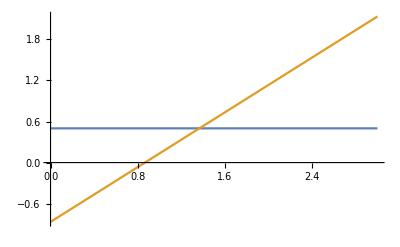

```mathematica
Plot[{Re[del[G, 1]], Im[del[G, 1]]}, {G, 0, 3}]
```

```mathematica
FullSimplify[Re[del[G,J]], Assumptions->{G>0, J>0}]
```

J

```mathematica
FullSimplify[Im[del[G,J]], Assumptions->{G>0, J>0}]
```

G+2 J Im[Cot[1/4 (π+2 ⅈ Log[2+√3])]]

```mathematica
Solve[]
```

```mathematica
FullSimplify[2 Im[Cot[1/4 (π+2 ⅈ Log[2+√3])]]]
```

-√3

```mathematica
FullSimplify[(1+(Sin[aR]/Cosh[aI])^4 +( Sinh[aI]/Cosh[aI])^4 + (Cos[aR]/Cosh[aI])^4)/2 , Assumptions->{aR!=0, aI!=0}]
```

1/8 (6+Cos[4 aR]+Cosh[4 aI]) Sech[aI]^4

```mathematica
aR [Jx_, Jy_, δ_, Γ_]=FullSimplify[ Re[ArcTan[Abs[(Jx + I Jy)]2,(δ - I Γ)]], Assumptions->{Jx>0, Jy>0, δ>0, Γ>0}]
aI[Jx_, Jy_, δ_, Γ_]= Im[ArcTan[Abs[(Jx + I Jy)]2,(δ - I Γ)]]
```

Re[ArcTan[2 Abs[Jx+ⅈ Jy],-ⅈ Γ+δ]]

Im[ArcTan[2 Abs[Jx+ⅈ Jy],-ⅈ Γ+δ]]

```mathematica
FullSimplify[1+(Sin[aR[J/Sqrt[2], J/Sqrt[2], 0, Γ]]/Cosh[aI[J/Sqrt[2], J/Sqrt[2], 0, Γ]])^4 +( Sinh[aI[J/Sqrt[2], J/Sqrt[2], 0, Γ]]/Cosh[aI[J/Sqrt[2], J/Sqrt[2], 0, Γ]])^4 + (Cos[aR[J/Sqrt[2], J/Sqrt[2], 0, Γ]]/Cosh[aI[J/Sqrt[2], J/Sqrt[2], 0, Γ]])^4/.{J->1}, Assumptions->{J>0, Γ>0 , Γ<2}]
```

1/4 (6+Cos[4 Re[ArcTan[(-1)^(1/4),-ⅈ Γ]]]+Cosh[4 Im[ArcTan[(-1)^(1/4),-ⅈ Γ]]]) Sech[Im[ArcTan[(-1)^(1/4),-ⅈ Γ]]]^4

```mathematica
H[G_, V_]=KroneckerProduct[{{0, 1},{1, -I G}}, IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],{{0, 1},{1, -I G}}]+ V KroneckerProduct[{{0,1},{0,0}}, {{0,0},{1,0}}]+V KroneckerProduct[{{0,0},{1,0}}, {{0,1},{0,0}}]
```

{{0,1,1,0},{1,-ⅈ G,V,1},{1,V,-ⅈ G,1},{0,1,1,-2 ⅈ G}}

```mathematica
Eigensystem[H[G, V]]
```

{{-ⅈ G-V,Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1],Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2],Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]},{{0,-1,1,0},{(ⅈ (2 G-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]))/Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1],-((2 G-2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]-2 ⅈ G^2 Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]-3 G Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]^2+ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]^3)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1])),-((-2 G+2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]-2 G V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]+ⅈ V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]^2)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,1])),1},{(ⅈ (2 G-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]))/Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2],-((2 G-2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]-2 ⅈ G^2 Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]-3 G Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]^2+ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]^3)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2])),-((-2 G+2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]-2 G V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]+ⅈ V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]^2)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,2])),1},{(ⅈ (2 G-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]))/Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3],-((2 G-2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]-2 ⅈ G^2 Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]-3 G Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]^2+ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]^3)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3])),-((-2 G+2 ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]-2 G V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]+ⅈ V Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]^2)/((G-ⅈ V-ⅈ Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3]) Root[-4 ⅈ G+(-4-2 G^2-2 ⅈ G V) #1+(3 ⅈ G-V) #1^2+#1^3&,3])),1}}}

```mathematica
M2[Jx_, Jy_, δ_,Γ_]:= -Log2[(6 + Cos[4 aR[Jx, Jy, δ, Γ]]+Cosh[4 aI[Jx, Jy, δ, Γ]])/(8 Cosh[aI[Jx, Jy, δ, Γ]]^4)]
```

```mathematica
FullSimplify[Sin[aR[1, 0,δ, Γ]]/Cosh[aI[1, 0,δ, Γ]], Assumptions->{J>0, δ>0, Γ>0}]
```

Sech[Re[ArcTanh[Γ+ⅈ δ]]] Sin[Im[ArcTanh[Γ+ⅈ δ]]]

```mathematica
Plot3D[{M2[1, 0, δ, Γ]}, {δ, -2, 2}, {Γ, 0, 4}]
```

-Graphics3D-

```mathematica
Plot3D[{M2c[1/Sqrt[2], 1/Sqrt[2], δ, Γ]}, {δ, -2, 2}, {Γ, 0, 4}]
```

-Graphics3D-

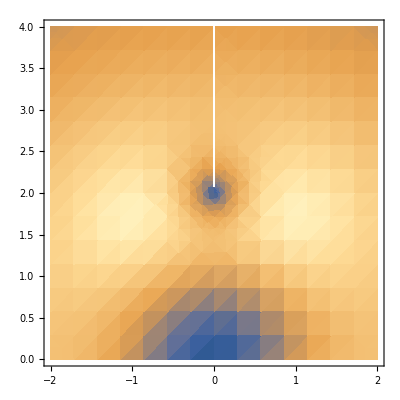

```mathematica
DensityPlot[{M2[1, 0, δ, Γ]}, {δ, -2, 2}, {Γ, 0, 4}]
```

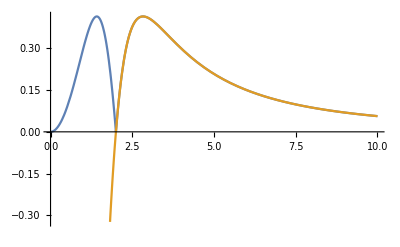

```mathematica
Plot[{M2[1,0, 0, G], -Log2[1 - 4 (G^2 - 4)/G^4]}, {G, 0, 10}]
```

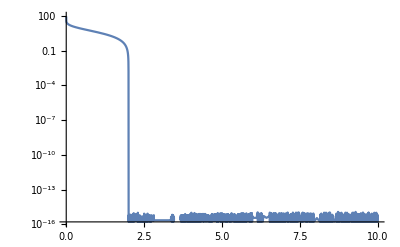

```mathematica
LogPlot[{Abs[M2[1,0, 0, G]+Log2[1 - 4 (G^2 - 4)/G^4]]}, {G, 0, 10}]
```

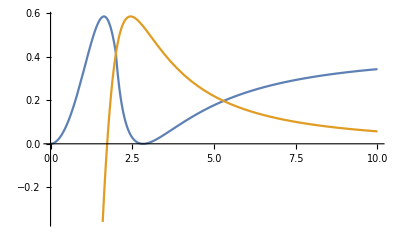

```mathematica
Plot[{M2c[1/Sqrt[2],1/Sqrt[2], 0, G], -Log2[1 - 4 (G^2 - 3)/G^4]}, {G, 0, 10}]
```

```mathematica
DSolve[{I D[α[t], t]/2 == J  - I Γ/Tan[α[t]/2] }, α[t], t]
```

DSolve::dsfun: InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[Times[«2»]+Times[«2»]]+J #1)/(J^2-Plus[«2»]^2)&][-2 ⅈ t+1] cannot be used as a function.

DSolve[{(J^2-(Γ+ⅈ δ)^2)/(J+(2 ⅈ (Γ+ⅈ δ) (1/2 J Cos[1/2 InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]]-1/2 (-ⅈ Γ+δ) Sin[1/2 InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]]))/((-ⅈ Γ+δ) Cos[1/2 InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]]+J Sin[1/2 InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]]))==J-ⅈ Γ Cot[1/2 InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]]},InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]],t]

```mathematica
α[t_]:=InverseFunction[(2 ⅈ (Γ+ⅈ δ) Log[(-ⅈ Γ+δ) Cos[#1/2]+J Sin[#1/2]]+J #1)/(J^2-(Γ+ⅈ δ)^2)&][-2 ⅈ t+C[1]]
```

```mathematica
e[δ_, J_, ]
```

```mathematica
Eigensystem[{{0, Jx-I Jy},{Jx + I Jy, δ - I Γ}}]
```

{{1/2 (-ⅈ Γ+δ-√(4 Jx^2+4 Jy^2-Γ^2-2 ⅈ Γ δ+δ^2)),1/2 (-ⅈ Γ+δ+√(4 Jx^2+4 Jy^2-Γ^2-2 ⅈ Γ δ+δ^2))},{{-(-ⅈ Γ+δ+√(4 Jx^2+4 Jy^2-Γ^2-2 ⅈ Γ δ+δ^2))/(2 (Jx+ⅈ Jy)),1},{-(-ⅈ Γ+δ-√(4 Jx^2+4 Jy^2-Γ^2-2 ⅈ Γ δ+δ^2))/(2 (Jx+ⅈ Jy)),1}}}

```mathematica
FullSimplify[TrigReduce[{Exp[I ϕ/2]Cos[(αR -I αI)/2],Exp[-I ϕ/2] Sin[(αR -I αI)/2]}.{{0, 1},{1,0}}.{Exp[-I ϕ/2]Cos[(αR +I αI)/2],Exp[I ϕ/2] Sin[(αR +I αI)/2]}], Assumptions->{αR!=0 ,αI!=0, ϕ>0}]
```

Cos[ϕ] Sin[αR]-Sin[ϕ] Sinh[αI]

```mathematica
FullSimplify[TrigReduce[{Exp[I ϕ/2]Cos[(αR -I αI)/2],Exp[-I ϕ/2] Sin[(αR -I αI)/2]}.{{0, -I},{I,0}}.{Exp[-I ϕ/2]Cos[(αR +I αI)/2],Exp[I ϕ/2] Sin[(αR +I αI)/2]}], Assumptions->{αR>0 ,αI>0, ϕ>0}]
```

Sin[αR] Sin[ϕ]+Cos[ϕ] Sinh[αI]

```mathematica
FullSimplify[TrigReduce[{Exp[I ϕ/2]Cos[(αR -I αI)/2],Exp[-I ϕ/2] Sin[(αR -I αI)/2]}.{{1, 0},{0,-1}}.{Exp[-I ϕ/2]Cos[(αR +I αI)/2],Exp[I ϕ/2] Sin[(αR +I αI)/2]}], Assumptions->{αR>0 ,αI>0, ϕ>0}]
```

Cos[αR]

```mathematica
FullSimplify[(1+((Cos[ϕ] Sin[αR]-Sin[ϕ] Sinh[αI])/Cosh[αI])^4 +((Sin[αR] Sin[ϕ]+Cos[ϕ] Sinh[αI])/Cosh[αI])^4 + (Cos[αR]/Cosh[αI])^4)/2 , Assumptions->{αR>0, αI>0, ϕ>0}]
```

1/2 (1+Cos[αR]^4 Sech[αI]^4+(Sech[αI] Sin[αR] Sin[ϕ]+Cos[ϕ] Tanh[αI])^4+(Cos[ϕ] Sech[αI] Sin[αR]-Sin[ϕ] Tanh[αI])^4)

```mathematica
FullSimplify[(Sin[αR] Sin[ϕ]+ Cos[ϕ]Sinh[αI])^4 +(Cos[αR] Sin[ϕ]- Cos[ϕ]Sinh[αI])^4  , Assumptions->{αR>0, αI>0, ϕ>0}]
```

(Cos[αR] Sin[ϕ]-Cos[ϕ] Sinh[αI])^4+(Sin[αR] Sin[ϕ]+Cos[ϕ] Sinh[αI])^4

```mathematica
(Sin[αR] Sin[ϕ]+ Cos[ϕ]Sinh[αI])^4 +(Cos[αR] Sin[ϕ]- Cos[ϕ]Sinh[αI])^4//TrigReduce//Simplify
```

1/64 (12+6 Cos[4 αR]-4 Cos[4 αR-2 ϕ]+Cos[4 (αR-ϕ)]+36 Cos[4 ϕ]+Cos[4 (αR+ϕ)]-4 Cos[2 (2 αR+ϕ)]+6 Cosh[4 αI]+12 ⅈ Cosh[αI+ⅈ (αR-4 ϕ)]-2 ⅈ Cosh[3 αI+ⅈ (αR-4 ϕ)]-4 ⅈ Cosh[3 αI+ⅈ (αR-2 ϕ)]-16 Cosh[2 (αI-ⅈ ϕ)]+Cosh[4 (αI-ⅈ ϕ)]-16 Cosh[2 (αI+ⅈ ϕ)]+Cosh[4 (αI+ⅈ ϕ)]-16 Cosh[2 (αI-2 ⅈ ϕ)]+4 Cosh[4 αI-2 ⅈ ϕ]-4 ⅈ Cosh[αI-3 ⅈ αR-2 ⅈ ϕ]-4 ⅈ Cosh[αI+3 ⅈ αR-2 ⅈ ϕ]-16 Cosh[2 (αI+2 ⅈ ϕ)]+4 Cosh[4 αI+2 ⅈ ϕ]+4 ⅈ Cosh[3 αI-ⅈ αR+2 ⅈ ϕ]+4 ⅈ Cosh[αI-3 ⅈ αR+2 ⅈ ϕ]+4 ⅈ Cosh[αI+3 ⅈ αR+2 ⅈ ϕ]+2 ⅈ Cosh[αI-3 ⅈ αR-4 ⅈ ϕ]+2 ⅈ Cosh[αI+3 ⅈ αR-4 ⅈ ϕ]-12 ⅈ Cosh[αI-ⅈ αR+4 ⅈ ϕ]+2 ⅈ Cosh[3 αI-ⅈ αR+4 ⅈ ϕ]-2 ⅈ Cosh[αI-3 ⅈ αR+4 ⅈ ϕ]-2 ⅈ Cosh[αI+3 ⅈ αR+4 ⅈ ϕ]-4 ⅈ Cosh[3 αI-ⅈ (αR+2 ϕ)]+4 ⅈ Cosh[3 αI+ⅈ (αR+2 ϕ)]+12 ⅈ Cosh[αI-ⅈ (αR+4 ϕ)]-2 ⅈ Cosh[3 αI-ⅈ (αR+4 ϕ)]-12 ⅈ Cosh[αI+ⅈ (αR+4 ϕ)]+2 ⅈ Cosh[3 αI+ⅈ (αR+4 ϕ)]-12 Sinh[αI+ⅈ (αR-4 ϕ)]+2 Sinh[3 αI+ⅈ (αR-4 ϕ)]+4 Sinh[3 αI+ⅈ (αR-2 ϕ)]+4 Sinh[αI-3 ⅈ αR-2 ⅈ ϕ]-4 Sinh[αI+3 ⅈ αR-2 ⅈ ϕ]+4 Sinh[3 αI-ⅈ αR+2 ⅈ ϕ]-4 Sinh[αI-3 ⅈ αR+2 ⅈ ϕ]+4 Sinh[αI+3 ⅈ αR+2 ⅈ ϕ]-2 Sinh[αI-3 ⅈ αR-4 ⅈ ϕ]+2 Sinh[αI+3 ⅈ αR-4 ⅈ ϕ]-12 Sinh[αI-ⅈ αR+4 ⅈ ϕ]+2 Sinh[3 αI-ⅈ αR+4 ⅈ ϕ]+2 Sinh[αI-3 ⅈ αR+4 ⅈ ϕ]-2 Sinh[αI+3 ⅈ αR+4 ⅈ ϕ]-4 Sinh[3 αI-ⅈ (αR+2 ϕ)]-4 Sinh[3 αI+ⅈ (αR+2 ϕ)]+12 Sinh[αI-ⅈ (αR+4 ϕ)]-2 Sinh[3 αI-ⅈ (αR+4 ϕ)]+12 Sinh[αI+ⅈ (αR+4 ϕ)]-2 Sinh[3 αI+ⅈ (αR+4 ϕ)])

```mathematica
ϕJ[Jx_, Jy_]:= ArcTan[-Jy, Jx]
```

```mathematica
M2c[Jx_, Jy_, δ_,Γ_]:=-Log2[1/2 (1+Cos[aR[Jx, Jy, δ, Γ]]^4 Sech[aI[Jx, Jy, δ, Γ]]^4+(Sech[aI[Jx, Jy, δ, Γ]] Sin[aR[Jx, Jy, δ, Γ]] Sin[ϕJ[Jx, Jy]]+Cos[ϕJ[Jx, Jy]] Tanh[aI[Jx, Jy, δ, Γ]])^4+(Cos[ϕJ[Jx, Jy]] Sech[aI[Jx, Jy, δ, Γ]] Sin[aR[Jx, Jy, δ, Γ]]-Sin[ϕJ[Jx, Jy]] Tanh[aI[Jx, Jy, δ, Γ]])^4)]
```

```mathematica
Eigensystem[{{+I G, J},{J, -I G}}]
```

{{-√(-G^2+J^2),√(-G^2+J^2)},{{-(-ⅈ G+√(-G^2+J^2))/J,1},{-(-ⅈ G-√(-G^2+J^2))/J,1}}}

```mathematica
Eigensystem[{{-I G, J},{J, +I G}}]
```

{{-√(-G^2+J^2),√(-G^2+J^2)},{{-(ⅈ G+√(-G^2+J^2))/J,1},{-(ⅈ G-√(-G^2+J^2))/J,1}}}

```mathematica
propt[t_]=FullSimplify[MatrixExp[-I {{0, (1-I)/Sqrt[2]},{(1+I)/Sqrt[2], -I Sqrt[6]}}t ], Assumptions->{G>0, t>0}]
```

{{1/2 ⅇ^(-√(2+√3) t) (1-√3+(1+√3) ⅇ^(√2 t)),(-1/2-ⅈ/2) ⅇ^(-√(2+√3) t) (-1+ⅇ^(√2 t))},{(1/2-ⅈ/2) ⅇ^(-√(2+√3) t) (-1+ⅇ^(√2 t)),1/2 ⅇ^(-√(2+√3) t) (1+√3-(-1+√3) ⅇ^(√2 t))}}

```mathematica
Limit[propt[t]/Tr[propt[t]], t->Infinity]
```

{{1/2 (1+√3),-1/2-ⅈ/2},{1/2-ⅈ/2,1/2-(√3)/2}}

```mathematica
FullSimplify[MatrixExp[-I {{0, 1},{1, -I Sqrt[8]}}t ], Assumptions->{G>0, t>0}]
```

{{ⅇ^(-√2 t) (Cosh[t]+√2 Sinh[t]),-ⅈ ⅇ^(-√2 t) Sinh[t]},{-ⅈ ⅇ^(-√2 t) Sinh[t],ⅇ^(-√2 t) (Cosh[t]-√2 Sinh[t])}}

```mathematica
Eigenvalues[{{1,-(1+ⅈ)/(1+√3)},{(1-ⅈ)/(1+√3),-2+√3}}]
```

{2/(1+√3),0}